Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

April 21, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Case Study: Serotonin Transporter Chemical Transformations

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of March 27, 2018, we used StarDrop and Nova to identify chemical transformations that are more likely to lead to new drugs that have a high potential for inhibiting a pathway known as the serotonin transporter pathway, which is used by a class of drugs known as SSRIs.

### Introduction/Background Information:

The following tech memo focuses on antidepressants. This is a large category of drugs which can be further categorized based on the way that they work. They include tricyclic, monoamine oxidase inhibitors, and selective serotonin reuptake inhibitors. The majority of antidepressants work by presenting the reuptake of neurotransmitters such as serotonin and dopamine in the brain. [1]

Selective serotonin reuptake inhibitors, otherwise known as SSRIs, inhibit the receptors that take serotonin from the space between neurons and consequently break it down. Serotonin is a neurotransmitter in the brain that plays a role in a person’s mood and other processes such as reward, learning, and memory. Lower or abnormal amounts of serotonin has the potential to lead to negative moods and a less happy feeling. However, it is also possible to have too much serotonin, which can lead to something known as serotonin syndrome. Serotonin syndrome almost only occurs when individuals overdose on SSRIs, and can be both toxic and fatal. [2]

## Methodology

For this study, the following analyses were conducted:

A drug profile was built for Sertraline

Lead drugs were imported into StarDrop and a set of chemical transformations was applied.

The chemical transformation data was filtered and cleaned.

A transformation was chosen based on the incidence rate in the dataset, and further analysis was performed.

## Results

### Drug Profile

A drug profile was built for Sertraline, including information such as the number of rotatable bonds and the logP value. This data can be found in the table below. The solubility was calculated using the Lemke Empirical Solubility rules. In the logBB/solubility lab, the logBB values were predicted using the Abraham equation. However, since we do not know the Abraham solvation parameters for Sertraline, a new linear regression was built using the predicted logBB values and other parameters such as number of hydrogen acceptors, logP, molecular weight, number of rotatable bonds and TPSA. Given these parameters, a  QSAR model was built with an R^2 value of .82. Using this equation, the logBB for Sertraline was predicted. StarDrop provides a value of 0.8325 for the logBB value. Therefore, if the value calculated by StarDrop is treated as the ground truth, the predicted value using the QSAR model has a percent error of 1.1%.

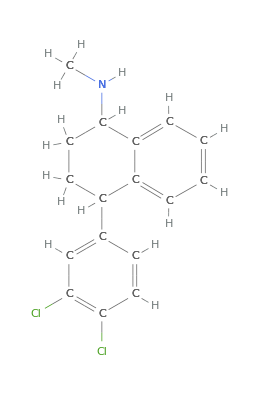
Formula | C_17H_17Cl_2N
IUPAC Name | (1S,4S)-4-(3,4-dichlorophenyl)-N-methyl-1,2,3,4-tetrahydronaphthalen-1-amine
Structural Formula | -Graphics-
Percent composition | {{C,66.68},{Cl,23.2},{H,5.6},{N,4.574}}
Molecular Weight (g/mol) | 306.2 u
Number of rotatable bonds | 2
Number of Rings | 3
pKa | 9.85
logP | 5.06
TPSA | 12 Å^2
Hydrogen donors | 1
Hydrogen acceptors | 1
SMILES formula | CNC1CCC(C2=CC=CC=C12)C3=CC(=C(C=C3)Cl)Cl
Classification of compound | {drugs,solid compounds,aromatics,chiral compounds}
List of Functional Groups | alkyl halide, alkane, phenyl, amide
Solubility Based on  Lemke empirical Solubility | Insoluble
Log BB using Abraham Solvation Parameter Equation | 0.84212

```mathematica
mylogbbFunction[accept1_,logP1_,mw1_,rotate1_,tpsa1_]=0.08581299700099981accept1+0.16141311295125144logP1-0.0012102624658333419mw1+0.05365220421307402rotate1-0.016715416069318284tpsa1+0.4034195491154515;

Grid[{{"Formula", ChemicalData["Sertraline","Formula"]}, {"IUPAC Name", ChemicalData["Sertraline","IUPACName"]}, {"Structural Formula", ChemicalData["Sertraline","CHColorStructureDiagram"]}, {"Percent composition", ChemicalData["Sertraline","ElementMassFraction"]}, {"Molecular Weight (g/mol)", ChemicalData["Sertraline","MolecularWeight"]}, {"Number of rotatable bonds", ChemicalData["Sertraline","RotatableBondCount"]}, {"Number of Rings", 3}, {"pKa", 9.85}, {"logP", 5.06}, {"TPSA", ChemicalData["Sertraline","TopologicalPolarSurfaceArea"]}, {"Hydrogen donors", ChemicalData["Sertraline","HBondDonorCount"]}, {"Hydrogen acceptors", ChemicalData["Sertraline","HBondAcceptorCount"]}, {"SMILES formula", ChemicalData["Sertraline","SMILES"]}, {"Classification of compound", ChemicalData["Sertraline","Memberships"]}, {"List of Functional Groups", "alkyl halide, alkane, phenyl, amide"}, {"Solubility Based on  Lemke empirical Solubility", "Insoluble"}, {"Log BB using Abraham Solvation Parameter Equation", mylogbbFunction[ChemicalData["Sertraline","HBondAcceptorCount"],5.06,306.2,
ChemicalData["Sertraline","RotatableBondCount"],12]}}, Frame -> All]
```

The journal article “Medicinal Chemical Properties of Successful Central Nervous System Drugs” provides a checklist for the parameters to be met for a compound to be a good CNS drug. Sertraline follows all the rules for parameters such as Number of H-bond donors, Number of H-bond acceptors, Number of rotatable bonds, Molecular Weight and TPSA, pKa. However, the cLogP for Sertraline is 5.35, which is slightly higher than the value of 5 listed in the checklist. Overall, Sertraline effectively follows most of the rules provided in the article. [3][4][5]

### Serotonin Transporter Biochemical Pathway

The pathway for SSRIs is summarized in the figure below. 5HT stands for 5-hydroxytryptamine, and is essentially the neurotransmitter serotonin. In the presynaptic neuron, TRP, which stands for tryptophan, is first converted to serotonin by the TPH and DDC genes. Then, serotonin is transported to the synaptic vesicle by the SLC18a2 gene, which undergoes exocytosis in order for the serotonin to travel to the synaptic cleft. Once in this area, a variety of different genes uptake the serotonin and through a series of steps, the transmitter is recycled into different parts. 

SSRIs work by inhibiting one of the genes that uptakes the serotonin in order to recycle it. Specifically, they inhibit the SLC6A4 gene, which transports the neurotransmitter from synaptic spaces into presynaptic neurons and later turns it off and recycles it. By inhibiting this gene, SSRIs ensure that the serotonin stays in the body for a longer time before it stops carrying out its biological processes. The serotonin also remains available to reach other neurons. [6]

-Graphics-

### StarDrop Nova Calculations

Using a set of three lead drug compounds, StarDrop Nova was used to apply a set of ring modifications to the original drug. Three different generations were created, and the 15 drug compounds with the lowest logKi for each generation was chosen and summarized in the table below.

```mathematica
drugData = Import["/Users/aakritilakshmanan/Downloads/NovaResults<3>.csv"];
viableDrug=drugData;
drugData // TableForm
```

Transform | Generation | Serotonin Transporter logKi
 | Gen0 | 1.087
Aromatic to pyrrole | Gen3 | 3.562
4-Pyridyl to 4-aniline | Gen2 | 3.934
NC-switch | Gen3 | 3.935
Aromatic to pyrrole | Gen2 | 3.957
Aromatic to pyrrole | Gen2 | 4.043
 | Gen0 | 4.045
Aromatic to thiophene | Gen2 | 4.045
4-Pyridyl to 4-aniline | Gen3 | 4.062
Aromatic to thiophene | Gen3 | 4.075
Aromatic to thiophene | Gen3 | 4.075
Aromatic carbon to pyridine nitrogen | Gen2 | 4.088
Six membered aromatic to furan | Gen2 | 4.101
Six membered aromatic to furan | Gen2 | 4.101
Aromatic carbon to pyridine nitrogen | Gen3 | 4.131
Aromatic to thiophene | Gen3 | 4.136
Aromatic carbon to pyridine nitrogen | Gen2 | 4.155
Aromatic to thiophene | Gen3 | 4.161
Aromatic to thiophene | Gen2 | 4.203
Pyridine to pyrrole | Gen1 | 4.214
Pyridine to thiophene | Gen1 | 4.22
NC-switch | Gen2 | 4.244
Aromatic carbon to pyridine nitrogen | Gen2 | 4.249
Aromatic to pyrrole | Gen3 | 4.271
Pyridine to pyrrole | Gen1 | 4.332
 | Gen0 | 4.333
Pyridine 1,2-switch | Gen1 | 4.333
Pyridine 1,3-switch | Gen1 | 4.333
Pyridine 1,4-switch | Gen1 | 4.361
Pyridine to thiophene | Gen1 | 4.374
Pyridine to furan | Gen1 | 4.387
Pyridine to furan | Gen1 | 4.389
Aromatic to thiophene | Gen1 | 4.449
Thiophene to benzene | Gen1 | 4.455
Pyridine nitrogen to aromatic carbon | Gen1 | 4.459
Aromatic to pyrrole | Gen1 | 4.475
Aromatic carbon to pyridine nitrogen | Gen1 | 4.525
Six membered aromatic to furan | Gen1 | 4.616

The drug with the lowest logKi value that was not a parent is pictured below:

### Narrative Results

Based on the Nova Calculations, the transformation that is most likely to result in a modification of the lead compounds to compounds that have a high likelihood of inhibiting the serotonin transport system is “Aromatic to thiophene,” since it occurs most in this list with 7 out of 45 compounds created through this transformation. This transformation is in the category of ring modifications, and the reference drug is Duloxetine. Fluoxetine, a drug that has been analyzed by Genez in the past, is related to Duloxetine. The SMIRKS for the transformation “Aromatic to thiophene” is as follows: [c:1]c([H])c([H])[c:2]>>[c:1]s[c:2]. Initially, the ring contains a chain of four carbons, shown by the “c” in the first part of the SMIRKS string: [c:1]c([H])c([H])[c:2]. After the transformation, the chain of four carbons turns into a chain of a carbon, sulfur, and then another carbon, shown by: [c:1]s[c:2]. This can be visualized further in the image below:

Duloxetine, otherwise known as Cymbalta, is used to treat depression, anxiety and neuropathic pain. It can also be used to treat chemotherapy-induced neuropathy. This drug works by reducing the reuptake of serotonin in the CNS and also increases the amount of dopamine in specific parts of the brain. Smoking can lead to a lower concentration of duloxetine. When the drug was first filed for FDA approval, experts were concerned by the drugs potential to cause liver toxicity and QTc interval prolongation, which plays a role in heart health. However, a later study found that the drug did not cause QTc interval prolongation, and warning for liver toxicity was placed on the drug. Drugs that end in -oxetine fall under the antidepressant class of drugs. [7]

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on April 14, 2021.  All references and resources are cited.  Assistance was provided by Mr. Gotwals.
  Electronic signature: -Graphics-

References:

1.	https://www.fda.gov/drugs/investigational-new-drug-ind-application/general-drug-categories
	2.	https://en.wikipedia.org/wiki/Serotonin#Nervous_system
	3.	https://www.ncbi.nlm.nih.gov/pmc/articles/PMC1201314/	
	4.	https://drugcentral.org/drugcard/2436
	5.	https://go.drugbank.com/drugs/DB01104
	6.	https://www.pharmgkb.org/pathway/PA161749006
	7.	https://en.wikipedia.org/wiki/Duloxetine